# Localization

## Robotics 11/6/15 Lauren Mitchell Tom Lillis Jordan Peters Emily Randall

```mathematica
Variance[{13,12,12,12,11,11,11,10,11,10,10,10,10,11,10,10,10,10,10,10,11,10,11,11,11,11,12,11,12,12,10,10,14,13,12,12,11,11,11,11,11,10,10,10,10,10,10,10,11,10,10,10,10,11,10,12,11,11,11,12,12,12,13,13,12,11,12,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,11,12,10,11,11,12,12,12,10,13,13,11,12,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,12,12,12,13,13,13,12,12,12,12,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,11,11,10,11,11,12,12,12,13,13,13,12,12,11,11,11,12,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,12}]

3122/3441
```

```mathematica
N[3122/3441]
```

0.907294

```mathematica
Variance[{23,21,22,22,22,22,22,22,21,22,21,22,22,21,22,22,21,22,22,22,21,21,22,21,22,21,22,22,22,22,21,22,22,22,22,21,21,22,22,22,21,20,19,22,22,22,22,22,22,22}]
```

1061/2450

```mathematica
N[1061/2450]
```

0.433061

```mathematica
Variance[{108,107,108,109,108,108,109,109,108,108,110,108,107,107,109,107,107,107,108,107,107,107,107,107,108,107,108,109,108,109,57,109,108,110,113,110,108,108,108,109,108,107,108,109,107,108,107,109,107,107,108,107,107,108,109,108,108,107,108,108,109,108,109,110,110,110,112,110,109,109,111,111}]
```

21703/568

```mathematica
N[21703/568]
```

38.2095

```mathematica
N[261899/1314]
```

199.314

```mathematica
Variance[{42,42,41,42,40,40,41,42,40,40,40,40,40,40,40,40,40,40,40,40,41,41,40,40,40,40,40,41,42,41,41,41,42,39,42,42,41,41,40,40,40,40,40,40,40,39,39,39,39,39,40,39,40,40,40,40,40,41,40,40,40,40,41,42,41,41,42,41,41,42,40,40,40,40,41,40,39,39,39,40,39,39,39,39,39,39,39,39,40,41,40,40,40,40,42,42,42,42,42,42,42,41,41,41,41,40,40,40,40,40,39,40,39,40,39,39,40,40,40,40,40,40,40,41,41,41,40,41,42,43,42,42,41,41,42,40,40,40,41,41,41,40,39,39,39,39,39,39,40,39,40,39,40,40,41,41,40,41,40,42,42,40,42,41,41,41,40,40,40,41,40,40,40,39,39,39,39,39,39,39,40,39,39,40,40,40,40,40,40,41,41,41,42}]
```

2125/2316

```mathematica
N[2125/2316]
```

0.91753

```mathematica
Variance[{31,31,31,31,32,32,32,32,32,32,32,30,31,31,31,32,32,32,32,31,32,32,31,32,32,30,30,30,30,32,30,30,30,30,31,31,31,31,31,31,31,30,30,30,30,31,31,31,32,30,30,30,31,30,31,31,31,31,31,31,31,31}]
```

34/61

```mathematica
N[34/61]
```

0.557377

```mathematica
Simplify[(1/2*(r1^2-(L^2+r1^2-r2^2)/(2*L))^(-0.5)*(2*r1-r1/L))^2+(0.5*(r1^2-(L^2+r1^2-r2^2)/(2*L))^(-0.5)*(r2/L))^2]
```

```mathematica
σy = (1. (0.5-1. L)^2 r1^2+0.25 r2^2)/(L^2 (r1^2-(L^2+r1^2-r2^2)/(2 L))^1.)
```

```mathematica
Simplify[(0.5*((L^2+r1^2-r2^2)/(2*L))^(-0.5)*(r1/L))^2+(0.5*((L^2+r1^2-r2^2)/(2*L))^(-0.5)*(r2/L))^2]
```

```mathematica
σx = (0.5000000000000001 r1^2+0.5000000000000001 r2^2)/(L^3+L r1^2-1. L r2^2)
```

```mathematica
distance = {10, 20, 30, 40};
variance = {0.907, 0.433, 0.557, 0.918};
data1 = Thread[{distance, variance}];
Grid[Prepend[data1, {"Distance (cm)", "Variance"}], Frame->All]
```

## 1)

Distance (cm) | Variance
10 | 0.907
20 | 0.433
30 | 0.557
40 | 0.918

```mathematica
f=(L^2+r1^2-r2^2)/(2*L);
σx = ((D[f,r1])^2+(D[f,r2])^2)*σr^2
```

(r1^2/L^2+r2^2/L^2) σr^2

```mathematica
g=Sqrt[r1^2-((L^2+r1^2-r2^2)/(2*L))^2];
σy = ((D[g,r1])^2+(D[g,r2])^2)*σr^2
```

((r2^2 (L^2+r1^2-r2^2)^2)/(4 L^4 (r1^2-((L^2+r1^2-r2^2)^2)/(4 L^2)))+((2 r1-(r1 (L^2+r1^2-r2^2))/L^2)^2)/(4 (r1^2-((L^2+r1^2-r2^2)^2)/(4 L^2)))) σr^2

2) σx^2 decreases as L increases, as does σy^2

3) We want to rely on this estimate when its varience is low or if we have used odemetry for a while (as accumulated error will be high), and odemetry when its varience is high. 
4) The distance measured will be higher than the actual distance. This will make the position estimate larger than it should be. To make up for this erorr, the robot would need to know the θ it is off from being orthogonal to the reflecting area and adjust the measurement accordingly. 

5) cos(θ) = (L^2+sqrt(x^2+y^2)^2-sqrt((x-L)^2+y^2))/(2Lsqrt(x^2+y^2))

```mathematica
cos(θ)=(L^2+Sqrt[(x^2+y^2)]^2-Sqrt[((x-L)^2+y^2)]/(2L Sqrt[x^2+y^2])
```

```mathematica
Plot3D[((r2^2 (L^2+r1^2-r2^2)^2)/(4 L^4 (r1^2-((L^2+r1^2-r2^2)^2)/(4 L^2)))+((2 r1-(r1 (L^2+r1^2-r2^2))/L^2)^2)/(4 (r1^2-((L^2+r1^2-r2^2)^2)/(4 L^2)))) σr^2,{L,-8,8},{σr,-8,8}]
```

-Graphics3D-

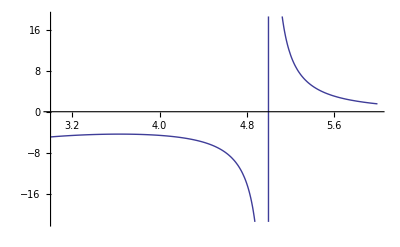

```mathematica
r1=10;r2=5;σr=0.5;
Plot[σy,{L,3,6}]
```

```mathematica
\
```